Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: 11369

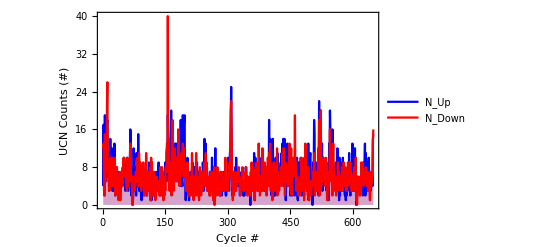

Number of Cycles: 696.

```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum=11369];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadata=ReadList[StringJoin[AscDir,"/",IntegerString[runNum,10,6],"/",IntegerString[runNum,10,6],"_Meta3.edm"],metaStructure2];
EDAListPlot[metadata[[2;;650,27]],metadata[[2;;650,28]],PlotLegends->{"N_Up","N_Down"},PlotStyle->{Blue,Red,Gray},Joined->True,Filling->Axis,PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Cycle #","UCN Counts (#)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000}]
Print["Number of Cycles: ",maxCy=metadata[[-1]][[2]]];
```

```mathematica
Clear[data,histdata2]
data={};
For[runi=1,runi<=maxCy,runi++,
If[runi≠ 11&&runi≠ 46&&runi≠ 117&&runi≠ 165&&runi≠ 188&&runi≠400&&runi≠420,
data=Join[data,ReadList[StringJoin[AscDir,"\\",IntegerString[runNum,10,6],"\\",IntegerString[runNum,10,6],"_UCNdet_",IntegerString[runi,10,3],"_0001.fast.ascii"],metaStructure]];
];
];
dimdata=Dimensions[data][[1]]
Dimensions[data]
```

149638

{149638,7}

## Studying timing difference between events

149637

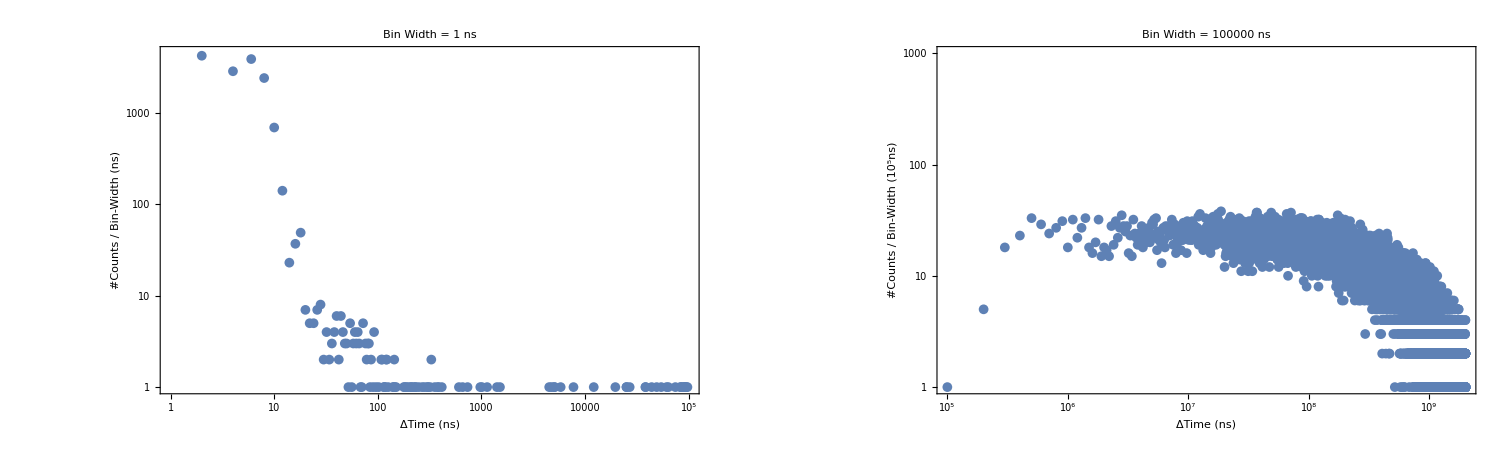

01_011369_timeStructure.png

```mathematica
tmdiff=(data[[2;;dimdata,4]]-data[[1;;dimdata-1,4]]);
Dimensions[tmdiff][[1]]
histbeg2=100000;histlast2=2000100000;binw2=100000;
hst2=HistogramList[tmdiff,{histbeg2,histlast2,binw2}];
histbeg=1;histlast=100001;binw=1;
hst=HistogramList[tmdiff,{histbeg,histlast,binw}];
pt1=ListLogLogPlot[Transpose[{hst[[1]][[1;;(histlast-histbeg)/binw]],hst[[2]]}],PlotRange->{{histbeg,histlast},{1,4500}},PlotMarkers->{Automatic,10},Frame->True,Joined->True,FrameLabel->{"ΔTime (ns)","#Counts / Bin-Width (ns)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{700},PlotLabel->StringJoin[(*"Total Number of Events = ",ToString[Total[hst[[2]]]],*)" Bin Width = ",ToString[binw]," ns"]];
hst2[[2]][[1;;2]]={1,5};
pt2=ListLogLogPlot[Transpose[{hst2[[1]][[1;;(histlast2-histbeg2)/binw2]],hst2[[2]]}],PlotRange->{{histbeg2,histlast2},{1,1000}},PlotMarkers->{Automatic,10},Frame->True,FrameLabel->{"ΔTime (ns)","#Counts / Bin-Width (10^5ns)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{700},PlotLabel->StringJoin[(*"Total Number of Events = ",ToString[Total[hst2[[2]]]],*)" Bin Width = ",ToString[binw2]," ns"]];
GraphicsGrid[{{pt1,pt2}}]
Export["01_011369_timeStructure.png",GraphicsGrid[{{pt1,pt2}}]]
```

```mathematica
Print["# of burst events: ",Dimensions[DeleteCases[cnt,0]][[1]]];
cleandata=Select[data[[1;;dimdata,{3,4,6,5,7}]],(#[[3]]-#[[4]])>145&];
Print["# of clean events: ",Dimensions[cleandata][[1]]];
Print["# of all events: ",Dimensions[data][[1]]];
Print["# Difference: ",Dimensions[data][[1]]-Dimensions[cleandata][[1]]];
Mean[data[[;;,6]]-data[[;;,5]]]
Max[data[[;;,6]]-data[[;;,5]]]
Min[data[[;;,6]]-data[[;;,5]]]
StandardDeviation[data[[;;,6]]-data[[;;,5]]]
```

# of burst events: 12123

# of clean events: 134627

# of all events: 149638

# Difference: 15011

337.183

5184.22

31.071

204.707

## Studying QDC events

Total Events: 141573

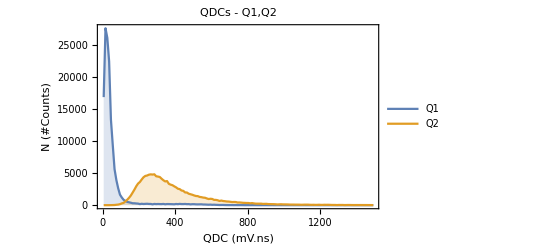

```mathematica
histbeg3=0;histlast3=1500;ChNum=4;binw3=10;
histdata=HistogramList[data[[1;;dimdata,5]],{histbeg3,histlast3,binw3}];
histdata2=HistogramList[data[[1;;dimdata,6]],{histbeg3,histlast3,binw3}];
ptdat=Table[{0,0},{k,1,Dimensions[histdata[[2]]][[1]]}];
ptdat2=Table[{0,0},{k,1,Dimensions[histdata2[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdata[[2]]][[1]],i++,
ptdat[[i]][[1]]=histdata[[1]][[i]]+((-histdata[[1]][[1]]+histdata[[1]][[2]])/2);
ptdat[[i]][[2]]=histdata[[2]][[i]];
ptdat2[[i]][[1]]=histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2);
ptdat2[[i]][[2]]=histdata2[[2]][[i]];
];
Print["Total Events: ",Total[histdata[[2]]]];
ListLinePlot[{ptdat,ptdat2},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"QDC (mV.ns)","N (#Counts)"},TicksStyle->Directive[FontSize->40],PlotLabel->"QDCs - Q1,Q2",PlotLegends->{"Q1","Q2"},Filling->Axis,ImageSize->{1000},TicksStyle->Directive[FontSize->40],LabelStyle->{18}]
```

```mathematica
dimdata=Dimensions[data][[1]];
cnt=Table[0,{k,1,dimdata}];j=1;
For[i=2,i≤dimdata,i++,
If[((data[[i]][[4]]-data[[i-1]][[4]]<1000)&&data[[i]][[3]]<10(*&&(data[[i]][[4]]>11500000000)&&(data[[i]][[4]]<12000000000)*)),
cnt[[j]]=i;
j++;
];
];
bdlst=DeleteCases[cnt,0];
bddata=Part[data,bdlst];
gddata=DeleteCases[data,Alternatives@@bddata];
Print["Total Events: ",Dimensions[data][[1]]];
Print["Bad Events: ",Dimensions[bddata][[1]]," , Good Events: ",Dimensions[gddata][[1]]," , Total Events: ",Dimensions[bddata][[1]]+Dimensions[gddata][[1]]];
(**)
gddimdata=Dimensions[gddata][[1]];bddimdata=Dimensions[bddata][[1]];
(**)
histdatagd=HistogramList[gddata[[1;;gddimdata,5]],{histbeg3,histlast3,binw3}];
histdatagd2=HistogramList[gddata[[1;;gddimdata,6]],{histbeg3,histlast3,binw3}];
histdatabd=HistogramList[gddata[[1;;bddimdata,5]],{histbeg3,histlast3,binw3}];
histdatabd2=HistogramList[gddata[[1;;bddimdata,6]],{histbeg3,histlast3,binw3}];
(**)
ptdatgd=Table[{0,0},{k,1,Dimensions[histdatagd[[2]]][[1]]}];
ptdatgd2=Table[{0,0},{k,1,Dimensions[histdatagd2[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdatagd[[2]]][[1]],i++,
ptdatgd[[i]][[1]]=histdatagd[[1]][[i]]+((-histdatagd[[1]][[1]]+histdatagd[[1]][[2]])/2);
ptdatgd[[i]][[2]]=histdatagd[[2]][[i]];
ptdatgd2[[i]][[1]]=histdatagd2[[1]][[i]]+((-histdatagd2[[1]][[1]]+histdatagd2[[1]][[2]])/2);
ptdatgd2[[i]][[2]]=histdatagd2[[2]][[i]];
];
(**)
ptdatbd=Table[{0,0},{k,1,Dimensions[histdatabd[[2]]][[1]]}];
ptdatbd2=Table[{0,0},{k,1,Dimensions[histdatabd2[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdatabd[[2]]][[1]],i++,
ptdatbd[[i]][[1]]=histdatabd[[1]][[i]]+((-histdatabd[[1]][[1]]+histdatabd[[1]][[2]])/2);
ptdatbd[[i]][[2]]=histdatabd[[2]][[i]];
ptdatbd2[[i]][[1]]=histdatabd2[[1]][[i]]+((-histdatabd2[[1]][[1]]+histdatabd2[[1]][[2]])/2);
ptdatbd2[[i]][[2]]=histdatabd2[[2]][[i]];
];
(**)
```

Total Events: 149638

Bad Events: 12123 , Good Events: 137515 , Total Events: 149638

Total good Events: 129884

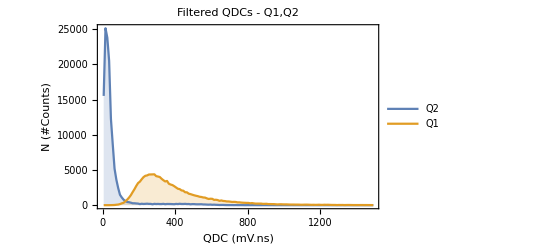

Total bad Events: 11439

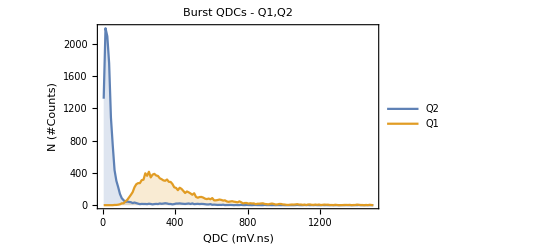

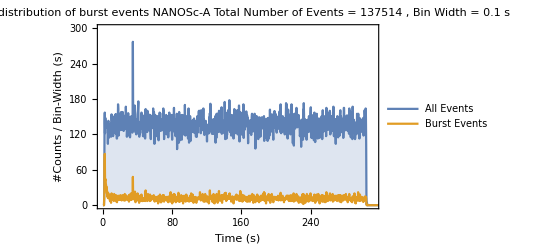

```mathematica
Print["Total good Events: ",Total[histdatagd[[2]]]];
ListLinePlot[{ptdatgd,ptdatgd2},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"QDC (mV.ns)","N (#Counts)"},TicksStyle->Directive[FontSize->40],PlotLabel->"Filtered QDCs - Q1,Q2",PlotLegends->{"Q2","Q1"},Filling->Axis,ImageSize->{1000},TicksStyle->Directive[FontSize->40],LabelStyle->{18}]
(**)
Print["Total bad Events: ",Total[histdatabd[[2]]]];
ListLinePlot[{ptdatbd,ptdatbd2},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"QDC (mV.ns)","N (#Counts)"},TicksStyle->Directive[FontSize->40],PlotLabel->"Burst QDCs - Q1,Q2",PlotLegends->{"Q2","Q1"},Filling->Axis,ImageSize->{1000},TicksStyle->Directive[FontSize->40],LabelStyle->{18}]
histbeg=100000000;histlast=302100000000;binw=100000000;
hst0=HistogramList[data[[2;;gddimdata,4]],{histbeg,histlast,binw}];
hst=HistogramList[gddata[[2;;gddimdata,4]],{histbeg,histlast,binw}];
hst2=HistogramList[bddata[[2;;bddimdata,4]],{histbeg,histlast,binw}];
ListPlot[{Transpose[{hst0[[1]][[1;;(histlast-histbeg)/binw]]*3/(10^9),hst0[[2]]}](*,Transpose[{hst[[1]][[1;;(histlast-histbeg)/binw]]/(10^9),hst[[2]]}]*),Transpose[{hst2[[1]][[1;;(histlast-histbeg)/binw]]*3/(10^9),hst2[[2]]}]},PlotRange->{{histbeg/(10^9),histlast/(10^9)+10},{0,300}},Joined->True,Frame->True,FrameLabel->{"Time (s)","#Counts / Bin-Width (s)"},TicksStyle->Directive[FontSize->40],PlotLegends->{"All Events","Burst Events"},LabelStyle->{18},ImageSize->{1000},Filling->True,PlotLabel->StringJoin["Time distribution of burst events \n NANOSc-A \n Total Number of Events = ",ToString[Total[hst[[2]]]]," , Bin Width = ",ToString[N[binw/(10^9)]]," s"]]
```

```mathematica
ucnshutter=Table[0,{k,1,310,.1}];
ucnshutter[[280;;300]]=1;
ucnshutter[[2180;;2200]]=-1;
```

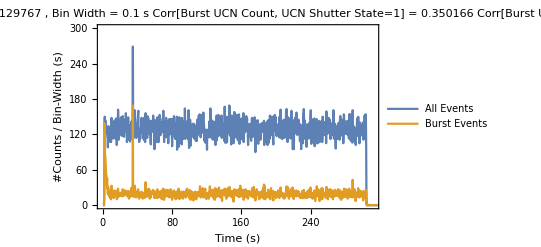
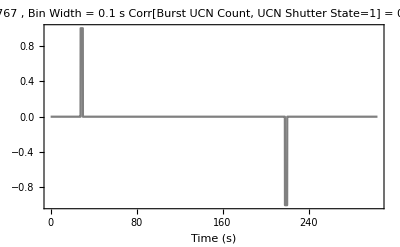

```mathematica
Overlay[{ListPlot[{Transpose[{hst0[[1]][[1;;(histlast-histbeg)/binw]]*3/(10^9),hst0[[2]]}](*,Transpose[{hst[[1]][[1;;(histlast-histbeg)/binw]]/(10^9),hst[[2]]}]*),Transpose[{hst2[[1]][[1;;(histlast-histbeg)/binw]]*3/(10^9),hst2[[2]]}]},ImagePadding->80,PlotRange->{{histbeg/(10^9),histlast/(10^9)+10},{0,300}},Joined->True,FrameLabel->{"Time (s)","#Counts / Bin-Width (s)"},TicksStyle->Directive[FontSize->40],PlotLegends->{"All Events","Burst Events"},LabelStyle->{18},ImageSize->{1000},Filling->{True,True},PlotLabel->StringJoin["Time distribution of burst events \n Total Number of Events = ",ToString[Total[hst[[2]]]]," , Bin Width = ",ToString[N[binw/(10^9)]]," s \n Corr[Burst UCN Count, UCN Shutter State=1] = ",ToString[N[Correlation[hst2[[2]][[20;;199]],100ucnshutter[[1;;540;;3]]]]],"\n Corr[Burst UCN Count, UCN Shutter State=-1] = ",ToString[N[Correlation[hst2[[2]][[220;;399]],100ucnshutter[[2001;;2540;;3]]]]]],Frame->{False,True,True,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}],
ListLinePlot[{Table[{k/10,ucnshutter[[k]]},{k,1,3040}]},ImagePadding->80,PlotStyle->Gray,Frame->{True,False,False,True},FrameTicks->All,FrameStyle->{Automatic,Automatic,Automatic,Gray},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},PlotLabel->StringJoin["Time distribution of burst events \n Total Number of Events = ",ToString[Total[hst[[2]]]]," , Bin Width = ",ToString[N[binw/(10^9)]]," s \n Corr[Burst UCN Count, UCN Shutter State=1] = ",ToString[N[Correlation[hst2[[2]][[20;;199]],100ucnshutter[[1;;540;;3]]]]],"\n Corr[Burst UCN Count, UCN Shutter State=-1] = ",ToString[N[Correlation[hst2[[2]][[220;;399]],100ucnshutter[[2001;;2540;;3]]]]]],FrameLabel->{"Time (s)","","",Rotate["UCN Shutter State {1=Opening, -1=Closing}",180Degree]}]}]
```

```mathematica
Print["Corr[Burst UCN Count, UCN Shutter State=1 (Opening)] = ",ToString[N[Correlation[hst2[[2]][[20;;199]],100ucnshutter[[1;;540;;3]]]]]];
Print["Corr[Burst UCN Count, UCN Shutter State=-1 (Closing)] = ",ToString[N[Correlation[hst2[[2]][[220;;399]],100ucnshutter[[2001;;2540;;3]]]]]];
```

Corr[Burst UCN Count, UCN Shutter State=1 (Opening)] = 0.350166

Corr[Burst UCN Count, UCN Shutter State=-1 (Closing)] = 0.0336673

## Leakage Current

Size of the file is = 82161

Size of the data set is = 300

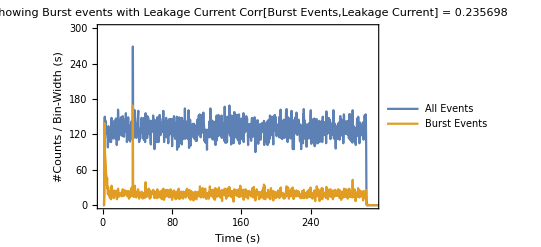
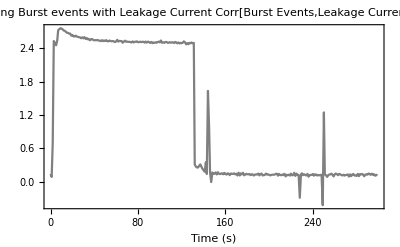

```mathematica
metaStructure3={Word,Real,Real,Real,Real,Real,Real};
lkgcur=ReadList[StringJoin[AscDir,"/",IntegerString[runNum,10,6],"/",IntegerString[runNum,10,6],"-0_Leakage_current3.edm"],metaStructure3];
Print["Size of the file is = ",Dimensions[lkgcur][[1]]];
datac=Table[{0,0},{k,1,300}];
Print["Size of the data set is = ",Dimensions[datac][[1]]];
For[k=1,k≤300,k++,
datac[[k]]={(AbsoluteTime[lkgcur[[k]][[1]]]-AbsoluteTime[lkgcur[[1]][[1]]]),lkgcur[[k]][[2]]};
];
Overlay[{ListPlot[{Transpose[{hst0[[1]][[1;;(histlast-histbeg)/binw]]*3/(10^9),hst0[[2]]}](*,Transpose[{hst[[1]][[1;;(histlast-histbeg)/binw]]/(10^9),hst[[2]]}]*),Transpose[{hst2[[1]][[1;;(histlast-histbeg)/binw]]*3/(10^9),hst2[[2]]}]},ImagePadding->80,PlotRange->{{histbeg/(10^9),histlast/(10^9)+10},{0,300}},Joined->True,FrameLabel->{"Time (s)","#Counts / Bin-Width (s)"},TicksStyle->Directive[FontSize->40],PlotLegends->{"All Events","Burst Events"},LabelStyle->{18},ImageSize->{1000},Filling->{True,True},PlotLabel->StringJoin["Plot showing Burst events with Leakage Current \n Corr[Burst Events,Leakage Current] = ",ToString[N[Correlation[hst2[[2]][[1;;300]],datac[[1;;300,2]]]]]],Frame->{False,True,True,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}],
ListLinePlot[{datac},ImagePadding->80,PlotStyle->Gray,Frame->{True,False,False,True},FrameTicks->All,FrameStyle->{Automatic,Automatic,Automatic,Gray},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},PlotLabel->StringJoin["Plot showing Burst events with Leakage Current \n Corr[Burst Events,Leakage Current] = ",ToString[N[Correlation[hst2[[2]][[1;;300]],datac[[1;;300,2]]]]]],FrameLabel->{"Time (s)","","",Rotate["Leakage Current (nA)",180Degree]}]}]
```

```mathematica
Correlation[hst2[[2]][[1;;300]],datac[[1;;300,2]]]
```

0.235698

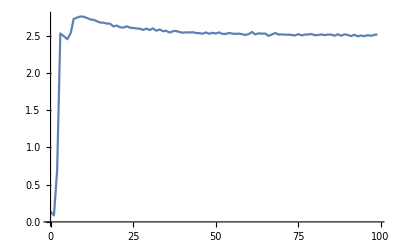

```mathematica
ListLinePlot[datac,PlotRange->Full]
```

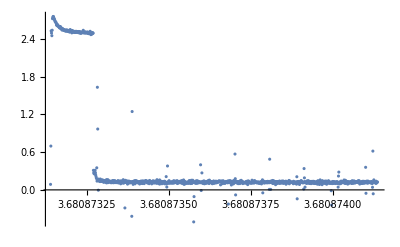

{{0.,0.14},{3.680873138573,0.088},{3.68087313954,0.697},{3.680873140501,2.529},{3.680873141556,2.494},{3.680873142623,2.452},{3.680873143678,2.539},{3.680873144532,2.723},{3.680873145586,2.743},{3.680873146652,2.758},{3.680873147497,2.754},{3.680873148571,2.738},{3.680873149626,2.717},{3.680873150691,2.711},{3.680873151535,2.695},{3.680873152586,2.676},{3.68087315365,2.674},{3.680873154495,2.663},{3.680873155559,2.661},{3.680873156624,2.624},{3.68087315768,2.636},{3.680873158534,2.613},{3.680873159588,2.609},{3.680873160654,2.625},{3.680873161499,2.609},{3.680873162563,2.603},{3.680873163619,2.597},{3.680873164683,2.592},{3.680873165527,2.578},{3.680873166592,2.594},{3.680873167647,2.576},{3.680873168501,2.598},{3.680873169556,2.567},{3.680873170622,2.583},{3.680873171676,2.559},{3.680873172519,2.567},{3.680873173584,2.542},{3.68087317465,2.56},{3.680873175495,2.565},{3.680873176561,2.549},{3.680873177615,2.54},{3.68087317868,2.545},{3.680873179525,2.543},{3.68087318058,2.547},{3.680873181644,2.535},{3.680873182488,2.536},{3.680873183554,2.526},{3.680873184608,2.543},{3.680873185672,2.526},{3.680873186517,2.538},{3.680873187592,2.53},{3.680873188646,2.544},{3.680873189501,2.525},{3.680873190555,2.523},{3.680873191621,2.537},{3.680873192673,2.527},{3.680873193518,2.524},{3.680873194582,2.528},{3.680873195637,2.519},{3.680873196501,2.509},{3.680873197556,2.522},{3.680873198631,2.55},{3.680873199475,2.518},{3.68087320054,2.53},{3.680873201594,2.528},{3.680873202649,2.527},{3.680873203504,2.497},{3.680873204558,2.516},{3.680873205624,2.535},{3.680873206677,2.515},{3.680873207532,2.518},{3.680873208586,2.513},{3.680873209652,2.514},{3.680873210496,2.51},{3.680873211561,2.503},{3.680873212617,2.521},{3.680873213691,2.503},{3.680873214537,2.515},{3.6808732156,2.516},{3.680873216655,2.522},{3.680873217499,2.507},{3.680873218564,2.509},{3.680873219619,2.516},{3.680873220684,2.508},{3.68087322153,2.515},{3.680873222593,2.514},{3.680873223648,2.5},{3.680873224513,2.519},{3.680873225567,2.5},{3.680873226632,2.517},{3.680873227476,2.512},{3.680873228541,2.494},{3.680873229597,2.512},{3.680873230662,2.491},{3.680873231506,2.502},{3.680873232571,2.494},{3.680873233626,2.506},{3.680873234673,2.498},{3.680873235517,2.51},{3.680873236582,2.517},{3.680873237637,2.504},{3.680873238502,2.538},{3.680873239556,2.498},{3.680873240622,2.503},{3.680873241675,2.496},{3.680873242531,2.509},{3.680873243584,2.513},{3.68087324465,2.497},{3.680873245494,2.496},{3.680873246548,2.508},{3.680873247614,2.498},{3.680873248667,2.506},{3.680873249522,2.502},{3.680873250577,2.493},{3.680873251642,2.511},{3.680873252486,2.505},{3.680873253551,2.487},{3.680873254606,2.503},{3.680873255672,2.484},{3.680873256515,2.495},{3.680873257581,2.49},{3.680873258639,2.5},{3.680873259494,2.522},{3.680873260548,2.506},{3.680873261624,2.469},{3.680873262688,2.489},{3.680873263542,2.472},{3.680873264597,2.495},{3.680873265663,2.487},{3.680873266506,2.502},{3.680873267572,2.488},{3.680873268626,2.494},{3.680873269481,0.311},{3.680873270536,0.273},{3.680873271601,0.256},{3.680873272656,0.259},{3.68087327352,0.289},{3.680873274575,0.312},{3.68087327564,0.27},{3.680873276484,0.235},{3.680873277549,0.209},{3.680873278604,0.182},{3.680873279669,0.351},{3.680873280514,0.14},{3.680873281568,1.632},{3.680873282633,0.968},{3.680873283477,0.172},{3.680873284542,-0.005},{3.680873285605,0.167},{3.680873286671,0.141},{3.680873287515,0.145},{3.680873288579,0.168},{3.680873289634,0.132},{3.680873290699,0.172},{3.680873291543,0.145},{3.68087329261,0.138},{3.680873293665,0.148},{3.680873294519,0.152},{3.680873295574,0.135},{3.680873296639,0.16},{3.680873297483,0.144},{3.680873298549,0.129},{3.680873299604,0.152},{3.680873300669,0.144},{3.680873301512,0.12},{3.680873302579,0.149},{3.680873303633,0.141},{3.680873304699,0.145},{3.680873305544,0.151},{3.680873306608,0.134},{3.680873307664,0.145},{3.680873308507,0.114},{3.680873309581,0.163},{3.680873310636,0.113},{3.68087331149,0.15},{3.680873312547,0.133},{3.680873313621,0.162},{3.680873314676,0.116},{3.680873315531,0.127},{3.680873316585,0.143},{3.68087331765,0.135},{3.680873318494,0.134},{3.680873319559,0.139},{3.680873320614,0.12},{3.680873321679,0.136},{3.680873322524,0.131},{3.680873323589,0.113},{3.680873324643,0.13},{3.680873325498,0.132},{3.680873326552,0.13},{3.680873327618,0.148},{3.680873328673,0.115},{3.680873329527,0.136},{3.680873330582,0.148},{3.680873331647,0.114},{3.680873332492,0.119},{3.680873333567,0.123},{3.680873334622,0.148},{3.680873335687,0.129},{3.680873336531,0.134},{3.680873337586,0.124},{3.680873338651,0.115},{3.680873339495,0.122},{3.68087334056,0.129},{3.680873341616,0.126},{3.680873342674,0.13},{3.68087334354,0.142},{3.680873344592,0.144},{3.680873345659,0.11},{3.680873346502,0.141},{3.680873347567,0.124},{3.680873348622,0.117},{3.680873349687,0.129},{3.680873350531,0.12},{3.680873351586,0.143},{3.680873352652,0.097},{3.680873353495,0.126},{3.68087335456,0.117},{3.680873355615,0.128},{3.68087335668,0.111},{3.680873357524,0.146},{3.68087335859,0.116},{3.680873359644,0.123},{3.680873360509,0.162},{3.680873361574,0.106},{3.680873362639,0.146},{3.680873363484,0.128},{3.680873364548,0.12},{3.680873365602,-0.287},{3.680873366668,0.133},{3.680873367511,0.152},{3.680873368577,0.118},{3.680873369632,0.135},{3.680873370697,0.12},{3.680873371542,0.114},{3.680873372595,0.142},{3.680873373662,0.092},{3.680873374505,0.123},{3.68087337557,0.121},{3.680873376625,0.126},{3.68087337769,0.14},{3.680873378534,0.11},{3.6808733796,0.134},{3.680873380655,0.128},{3.68087338151,0.113},{3.680873382565,0.123},{3.680873383631,0.115},{3.680873384684,0.123},{3.680873385539,0.126},{3.680873386593,-0.42},{3.680873387659,1.246},{3.680873388503,0.134},{3.680873389568,0.117},{3.680873390623,0.088},{3.680873391687,0.12},{3.680873392531,0.13},{3.680873393595,0.134},{3.680873394661,0.146},{3.680873395505,0.124},{3.680873396571,0.097},{3.680873397635,0.136},{3.68087339849,0.148},{3.680873399541,0.136},{3.680873400595,0.119},{3.680873401662,0.142},{3.680873402505,0.135},{3.68087340357,0.123},{3.680873404625,0.114},{3.680873405689,0.127},{3.680873406533,0.112},{3.680873407598,0.122},{3.680873408653,0.125},{3.68087340951,0.132},{3.680873410566,0.094},{3.680873411631,0.133},{3.680873412683,0.103},{3.680873413538,0.128},{3.680873414593,0.14},{3.680873415658,0.113},{3.680873416503,0.114},{3.680873417577,0.105},{3.680873418632,0.141},{3.680873419698,0.101},{3.680873420541,0.137},{3.680873421606,0.134},{3.680873422671,0.14},{3.680873423515,0.129},{3.680873424582,0.1},{3.680873425646,0.129},{3.68087342649,0.135},{3.680873427546,0.128},{3.68087342861,0.149},{3.680873429666,0.135},{3.68087343052,0.126},{3.680873431574,0.145},{3.680873432639,0.124},{3.680873433483,0.135},{3.680873434548,0.109},{3.680873435602,0.125},{3.680873436669,0.113},{3.680873437511,0.123},{3.680873438577,0.131},{3.680873439633,0.099},{3.680873440707,0.15},{3.680873441551,0.134},{3.680873442605,0.138},{3.680873443671,0.135},{3.680873444515,0.135},{3.68087344558,0.122},{3.680873446634,0.119},{3.68087344749,0.096},{3.680873448544,0.117},{3.680873449609,0.123},{3.680873450665,0.133},{3.680873451519,0.145},{3.680873452574,0.125},{3.68087345364,0.135},{3.680873454483,0.108},{3.680873455549,0.132},{3.680873456604,0.134},{3.68087345767,0.14},{3.680873458513,0.115},{3.68087345958,0.135},{3.680873460634,0.132},{3.680873461489,0.108},{3.680873462545,0.109},{3.68087346362,0.162},{3.680873464675,0.135},{3.68087346553,0.11},{3.680873466585,0.116},{3.680873467649,0.109},{3.680873468493,0.113},{3.68087346956,0.147},{3.680873470614,0.095},{3.680873471679,0.158},{3.680873472523,0.097},{3.680873473589,0.099},{3.680873474643,0.127},{3.680873475498,0.136},{3.680873476552,0.109},{3.680873477619,0.135},{3.680873478675,0.098},{3.680873479528,0.125},{3.680873480584,0.13},{3.680873481648,0.11},{3.680873482494,0.111},{3.680873483558,0.112},{3.680873484613,0.134},{3.680873485678,0.123},{3.680873486522,0.138},{3.680873487589,0.097},{3.680873488642,0.129},{3.680873489507,0.103},{3.680873490561,0.12},{3.680873491627,0.211},{3.680873492681,0.094},{3.680873493536,0.045},{3.680873494591,0.12},{3.680873495656,0.38},{3.6808734965,0.119},{3.680873497555,0.104},{3.68087349862,0.133},{3.680873499675,0.118},{3.680873500529,0.147},{3.680873501585,0.107},{3.68087350265,0.125},{3.680873503494,0.111},{3.68087350456,0.112},{3.680873505615,0.122},{3.68087350668,0.122},{3.680873507523,0.112},{3.680873508589,0.13},{3.680873509643,0.106},{3.680873510508,0.118},{3.680873511562,0.117},{3.680873512628,0.131},{3.680873513682,0.108},{3.680873514548,0.146},{3.680873515601,0.113},{3.680873516667,0.115},{3.68087351751,0.125},{3.680873518587,0.14},{3.68087351964,0.125},{3.680873520484,0.116},{3.68087352155,0.128},{3.680873522604,0.124},{3.68087352367,0.144},{3.680873524513,0.108},{3.680873525579,0.144},{3.680873526634,0.101},{3.680873527488,0.134},{3.680873528542,0.133},{3.680873529599,0.118},{3.680873530654,0.117},{3.680873531509,0.119},{3.680873532563,0.135},{3.68087353363,0.113},{3.680873534683,0.136},{3.680873535539,0.119},{3.680873536592,0.131},{3.680873537658,0.138},{3.680873538502,0.146},{3.680873539552,0.104},{3.680873540616,0.143},{3.680873541671,0.133},{3.680873542526,0.113},{3.680873543582,0.106},{3.680873544646,0.158},{3.68087354549,0.091},{3.680873546545,0.142},{3.68087354761,0.09},{3.680873548664,0.118},{3.680873549518,0.104},{3.680873550573,0.131},{3.680873551638,0.104},{3.680873552693,0.11},{3.680873553548,0.111},{3.680873554602,0.114},{3.680873555668,0.112},{3.680873556511,0.114},{3.680873557576,0.108},{3.680873558631,0.129},{3.680873559706,0.108},{3.68087356055,0.109},{3.680873561615,0.145},{3.680873562671,0.11},{3.680873563514,0.147},{3.68087356458,0.132},{3.680873565644,0.115},{3.680873566499,0.101},{3.680873567553,0.113},{3.68087356862,0.153},{3.680873569684,0.106},{3.68087357054,0.112},{3.680873571593,0.109},{3.68087357266,0.153},{3.680873573504,0.138},{3.680873574568,0.124},{3.680873575623,-0.509},{3.680873576688,-0.107},{3.680873577533,0.122},{3.680873578597,0.123},{3.680873579652,0.117},{3.680873580507,0.107},{3.680873581561,0.14},{3.680873582627,0.106},{3.680873583681,0.127},{3.680873584549,0.11},{3.680873585606,0.147},{3.680873586673,0.106},{3.680873587517,0.117},{3.680873588592,0.121},{3.680873589646,0.138},{3.68087359049,0.112},{3.680873591556,0.117},{3.680873592621,0.126},{3.680873593676,0.125},{3.680873594519,0.115},{3.680873595589,0.128},{3.680873596654,0.399},{3.680873597498,0.115},{3.680873598562,-0.01},{3.680873599618,0.113},{3.680873600684,0.27},{3.680873601527,0.132},{3.680873602592,0.116},{3.680873603646,0.135},{3.680873604502,0.101},{3.680873605565,0.139},{3.680873606632,0.104},{3.680873607686,0.141},{3.680873608529,0.097},{3.680873609596,0.133},{3.680873610649,0.121},{3.680873611504,0.109},{3.680873612571,0.109},{3.680873613644,0.107},{3.680873614699,0.124},{3.680873615554,0.126},{3.680873616609,0.136},{3.680873617674,0.11},{3.680873618519,0.127},{3.680873619583,0.142},{3.680873620639,0.119},{3.680873621492,0.15},{3.680873622548,0.101},{3.680873623612,0.155},{3.680873624667,0.113},{3.680873625521,0.136},{3.680873626576,0.131},{3.680873627651,0.118},{3.680873628496,0.117},{3.680873629549,0.131},{3.680873630614,0.133},{3.68087363167,0.11},{3.680873632524,0.098},{3.680873633579,0.104},{3.680873634644,0.125},{3.680873635488,0.116},{3.680873636554,0.142},{3.680873637608,0.104},{3.680873638674,0.121},{3.680873639518,0.128},{3.680873640593,0.114},{3.680873641646,0.112},{3.680873642501,0.125},{3.680873643567,0.139},{3.680873644631,0.116},{3.680873645685,0.113},{3.680873646529,0.133},{3.680873647595,0.121},{3.680873648649,0.127},{3.680873649505,0.127},{3.680873650559,0.136},{3.680873651624,0.124},{3.680873652679,0.144},{3.680873653533,0.135},{3.680873654589,0.13},{3.680873655653,0.14},{3.680873656499,0.136},{3.680873657575,0.08},{3.680873658629,0.135},{3.680873659696,0.129},{3.68087366054,0.142},{3.680873661605,0.107},{3.680873662659,0.134},{3.680873663515,0.099},{3.680873664568,0.136},{3.680873665645,0.145},{3.680873666699,0.132},{3.680873667556,0.108},{3.680873668608,0.116},{3.680873669674,0.108},{3.680873670518,0.125},{3.680873671584,0.105},{3.680873672639,0.114},{3.680873673492,0.121},{3.680873674547,0.135},{3.680873675612,0.122},{3.680873676667,0.125},{3.680873677531,0.129},{3.680873678587,0.132},{3.680873679651,0.112},{3.680873680495,0.143},{3.68087368156,-0.225},{3.680873682616,0.123},{3.680873683681,0.122},{3.680873684525,0.144},{3.68087368558,0.118},{3.680873686645,0.146},{3.680873687699,0.11},{3.680873688559,0.13},{3.680873689609,0.139},{3.680873690674,0.078},{3.680873691518,0.126},{3.680873692576,0.122},{3.680873693642,0.109},{3.680873694696,0.135},{3.680873695551,0.111},{3.680873696616,0.095},{3.680873697681,0.148},{3.680873698524,0.108},{3.680873699579,0.141},{3.680873700644,0.137},{3.680873701699,0.57},{3.680873702556,0.178},{3.680873703608,-0.08},{3.680873704674,0.119},{3.680873705518,0.138},{3.680873706583,0.111},{3.680873707639,0.122},{3.680873708492,0.127},{3.680873709548,0.11},{3.680873710612,0.132},{3.680873711667,0.099},{3.680873712531,0.13},{3.680873713586,0.115},{3.68087371465,0.12},{3.680873715494,0.129},{3.680873716549,0.1},{3.680873717615,0.144},{3.680873718669,0.115},{3.680873719523,0.125},{3.680873720578,0.152},{3.680873721644,0.117},{3.680873722698,0.137},{3.680873723553,0.111},{3.680873724607,0.118},{3.680873725673,0.1},{3.680873726517,0.127},{3.680873727583,0.121},{3.680873728637,0.112},{3.680873729491,0.12},{3.680873730546,0.111},{3.680873731611,0.117},{3.680873732666,0.121},{3.68087373352,0.109},{3.680873734575,0.126},{3.680873735641,0.119},{3.680873736695,0.135},{3.680873737549,0.101},{3.680873738614,0.114},{3.680873739669,0.138},{3.680873740524,0.084},{3.680873741578,0.133},{3.680873742653,0.143},{3.680873743497,0.124},{3.680873744563,0.123},{3.680873745617,0.127},{3.680873746692,0.123},{3.680873747536,0.107},{3.680873748602,0.119},{3.680873749656,0.113},{3.680873750511,0.114},{3.680873751565,0.119},{3.680873752642,0.105},{3.680873753695,0.154},{3.680873754539,0.115},{3.680873755605,0.118},{3.68087375667,0.118},{3.680873757514,0.131},{3.680873758568,0.109},{3.680873759634,0.14},{3.680873760688,0.112},{3.680873761543,0.147},{3.680873762598,0.135},{3.680873763663,0.136},{3.680873764507,0.12},{3.680873765571,0.12},{3.680873766626,0.127},{3.680873767691,0.112},{3.680873768535,0.117},{3.680873769601,0.122},{3.680873770655,0.111},{3.68087377151,0.122},{3.680873772574,0.127},{3.68087377364,0.115},{3.680873774694,0.105},{3.680873775544,0.112},{3.680873776604,0.121},{3.680873777658,0.105},{3.680873778513,0.124},{3.680873779567,0.113},{3.680873780633,0.125},{3.680873781685,0.13},{3.680873782528,0.095},{3.680873783594,0.13},{3.680873784648,0.115},{3.680873785503,0.16},{3.680873786558,-0.047},{3.680873787623,0.124},{3.680873788677,0.118},{3.680873789531,0.112},{3.680873790586,0.137},{3.680873791652,0.11},{3.680873792496,0.127},{3.68087379356,0.114},{3.680873794615,0.118},{3.68087379569,0.117},{3.680873796534,0.129},{3.680873797601,0.114},{3.680873798654,0.133},{3.680873799498,0.128},{3.680873800572,0.112},{3.68087380164,0.136},{3.680873802694,0.127},{3.680873803538,0.122},{3.680873804603,0.133},{3.680873805659,0.113},{3.680873806513,0.008},{3.680873807566,0.488},{3.680873808632,0.118},{3.680873809686,0.137},{3.680873810541,0.008},{3.680873811596,0.131},{3.680873812661,0.116},{3.680873813505,0.142},{3.68087381457,0.114},{3.680873815625,0.121},{3.68087381669,0.15},{3.680873817534,0.101},{3.6808738186,0.138},{3.680873819654,0.105},{3.680873820498,0.142},{3.680873821563,0.134},{3.680873822618,0.127},{3.680873823684,0.131},{3.680873824528,0.131},{3.680873825594,0.083},{3.680873826659,0.133},{3.680873827505,0.117},{3.680873828569,0.131},{3.680873829624,0.1},{3.68087383069,0.131},{3.680873831534,0.112},{3.680873832587,0.126},{3.680873833654,0.128},{3.680873834496,0.122},{3.680873835567,0.132},{3.680873836616,0.104},{3.680873837682,0.141},{3.680873838526,0.106},{3.680873839591,0.133},{3.680873840645,0.112},{3.6808738415,0.128},{3.680873842556,0.116},{3.68087384362,0.108},{3.680873844675,0.14},{3.68087384553,0.12},{3.680873846584,0.122},{3.680873847649,0.112},{3.680873848493,0.141},{3.680873849548,0.104},{3.680873850613,0.134},{3.680873851668,0.11},{3.680873852522,0.114},{3.680873853577,0.121},{3.680873854643,0.124},{3.680873855697,0.128},{3.680873856553,0.138},{3.680873857606,0.09},{3.680873858673,0.135},{3.680873859516,0.121},{3.68087386058,0.114},{3.680873861635,0.127},{3.680873862492,0.112},{3.680873863549,0.114},{3.680873864623,0.126},{3.680873865678,0.115},{3.680873866532,0.15},{3.680873867587,0.097},{3.680873868652,0.142},{3.680873869496,0.115},{3.680873870561,0.125},{3.680873871617,0.118},{3.680873872691,0.121},{3.680873873536,0.121},{3.680873874601,0.124},{3.680873875655,0.123},{3.68087387651,0.123},{3.680873877564,0.112},{3.68087387863,0.118},{3.680873879684,0.098},{3.680873880528,0.137},{3.680873881594,0.116},{3.680873882647,0.122},{3.680873883502,0.111},{3.680873884557,0.124},{3.680873885628,0.105},{3.680873886683,0.113},{3.680873887538,0.107},{3.680873888593,0.129},{3.680873889657,0.091},{3.680873890501,0.209},{3.680873891566,-0.142},{3.68087389262,0.128},{3.680873893686,0.129},{3.680873894529,0.121},{3.680873895584,0.134},{3.68087389665,0.124},{3.680873897715,0.123},{3.680873898571,0.086},{3.680873899623,0.123},{3.68087390069,0.126},{3.680873901532,0.127},{3.680873902598,0.132},{3.680873903653,0.149},{3.680873904518,0.125},{3.680873905571,0.137},{3.680873906637,0.114},{3.680873907691,0.127},{3.680873908547,0.114},{3.6808739096,0.123},{3.680873910675,0.113},{3.680873911519,0.013},{3.680873912572,0.339},{3.680873913638,0.191},{3.680873914693,0.133},{3.680873915553,0.044},{3.680873916612,0.113},{3.680873917679,0.119},{3.680873918522,0.123},{3.680873919586,0.12},{3.680873920642,0.102},{3.680873921707,0.143},{3.680873922551,0.123},{3.680873923616,0.114},{3.680873924671,0.117},{3.680873925526,0.147},{3.68087392658,0.113},{3.680873927646,0.135},{3.680873928699,0.102},{3.680873929544,0.132},{3.680873930609,0.103},{3.680873931663,0.134},{3.680873932525,0.108},{3.68087393359,0.1},{3.680873934644,0.122},{3.680873935498,0.101},{3.680873936553,0.135},{3.680873937618,0.134},{3.680873938673,0.132},{3.680873939529,0.133},{3.680873940582,0.136},{3.680873941648,0.107},{3.680873942703,0.135},{3.680873943562,0.101},{3.680873944618,0.122},{3.680873945673,0.112},{3.680873946528,0.113},{3.680873947582,0.127},{3.680873948648,0.101},{3.680873949703,0.121},{3.680873950558,0.128},{3.680873951612,0.1},{3.680873952677,0.131},{3.680873953522,0.091},{3.680873954585,0.145},{3.68087395564,0.117},{3.680873956705,0.138},{3.680873957549,0.1},{3.680873958614,0.129},{3.680873959679,0.086},{3.680873960524,0.13},{3.680873961598,0.159},{3.680873962653,0.135},{3.680873963507,0.128},{3.680873964562,0.119},{3.680873965628,0.116},{3.680873966683,0.128},{3.680873967536,0.083},{3.680873968591,0.147},{3.680873969656,0.103},{3.6808739705,0.13},{3.680873971566,0.114},{3.68087397262,0.116},{3.680873973686,0.126},{3.680873974529,0.125},{3.680873975583,0.107},{3.680873976649,0.14},{3.680873977703,0.101},{3.680873978567,0.123},{3.680873979624,0.124},{3.680873980689,0.14},{3.680873981533,0.09},{3.680873982625,0.122},{3.68087398368,0.116},{3.680873984534,0.113},{3.680873985599,0.124},{3.680873986664,0.14},{3.680873987508,0.144},{3.680873988564,0.105},{3.680873989628,0.126},{3.680873990683,0.107},{3.680873991537,0.122},{3.680873992592,0.122},{3.680873993657,0.103},{3.680873994501,0.11},{3.680873995567,-0.013},{3.680873996622,-0.242},{3.680873997687,0.128},{3.680873998531,0.1},{3.680873999595,0.115},{3.68087400065,0.134},{3.680874001715,0.103},{3.680874002559,0.115},{3.680874003624,0.133},{3.680874004679,0.108},{3.680874005523,0.112},{3.680874006588,0.124},{3.680874007643,0.116},{3.680874008497,0.101},{3.680874009561,0.126},{3.680874010628,0.123},{3.680874011683,0.119},{3.680874012549,0.129},{3.6808740136,0.102},{3.680874014665,0.129},{3.680874015508,0.108},{3.680874016564,0.044},{3.680874017628,0.22},{3.680874018683,0.283},{3.680874019537,0.112},{3.680874020592,0.095},{3.680874021657,0.121},{3.680874022501,0.112},{3.680874023567,0.131},{3.680874024622,0.1},{3.680874025687,0.14},{3.68087402653,0.134},{3.680874027595,0.119},{3.680874028649,0.114},{3.680874029702,0.13},{3.680874030557,0.134},{3.680874031612,0.133},{3.680874032677,0.129},{3.680874033521,0.113},{3.680874034595,0.157},{3.68087403565,0.13},{3.680874036715,0.134},{3.680874037559,0.103},{3.680874038624,0.153},{3.680874039679,0.103},{3.680874040523,0.123},{3.680874041588,0.139},{3.680874042643,0.126},{3.680874043497,0.128},{3.680874044552,0.132},{3.680874045618,0.093},{3.680874046673,0.133},{3.680874047528,0.099},{3.680874048581,0.106},{3.680874049647,0.116},{3.680874050701,0.114},{3.680874051556,0.122},{3.680874052616,0.12},{3.680874053671,0.132},{3.680874054526,0.115},{3.680874055579,0.114},{3.680874056646,0.129},{3.680874057699,0.102},{3.680874058555,0.128},{3.680874059609,0.146},{3.680874060674,0.108},{3.680874061518,0.118},{3.680874062572,0.106},{3.680874063638,0.137},{3.680874064693,0.113},{3.680874065548,0.142},{3.680874066602,0.112},{3.680874067668,0.133},{3.680874068512,0.112},{3.680874069577,0.115},{3.680874070633,0.128},{3.680874071697,0.13},{3.680874072557,0.131},{3.680874073612,0.132},{3.680874074676,0.129},{3.68087407552,0.122},{3.680874076575,0.116},{3.680874077638,0.144},{3.680874078693,0.117},{3.68087407955,0.146},{3.680874080602,0.122},{3.680874081667,0.141},{3.680874082511,0.093},{3.680874083576,0.107},{3.680874084631,0.105},{3.680874085696,0.116},{3.68087408654,0.105},{3.680874087606,0.12},{3.680874088658,0.109},{3.680874089502,0.134},{3.680874090577,0.103},{3.68087409163,0.111},{3.680874092696,0.138},{3.680874093539,0.108},{3.680874094605,0.132},{3.680874095659,0.118},{3.680874096514,0.108},{3.680874097569,0.135},{3.680874098634,0.111},{3.68087409969,0.129},{3.680874100532,0.359},{3.680874101598,-0.054},{3.680874102652,0.126},{3.680874103506,0.139},{3.680874104565,0.11},{3.680874105638,0.12},{3.680874106692,0.109},{3.680874107557,0.14},{3.680874108612,0.112},{3.680874109678,0.121},{3.680874110521,0.117},{3.680874111586,0.13},{3.680874112641,0.117},{3.680874113495,0.121},{3.68087411455,0.114},{3.680874115626,0.114},{3.680874116681,0.113},{3.680874117536,0.134},{3.68087411859,0.117},{3.680874119655,0.122},{3.680874120499,0.1},{3.680874121565,0.041},{3.680874122619,0.617},{3.680874123685,-0.062},{3.680874124529,0.138},{3.680874125604,0.159},{3.680874126658,0.116},{3.680874127514,0.123},{3.680874128577,0.12},{3.680874129643,0.12},{3.680874130697,0.122},{3.680874131542,0.103},{3.680874132623,0.138},{3.680874133679,0.109},{3.680874134523,0.118},{3.680874135587,0.12},{3.680874136642,0.126}}

```mathematica
ListPlot[lkgcur[[2;;1000,{1,2}]],PlotRange->Full]
lkgcur[[1;;1000,{1,2}]]
```